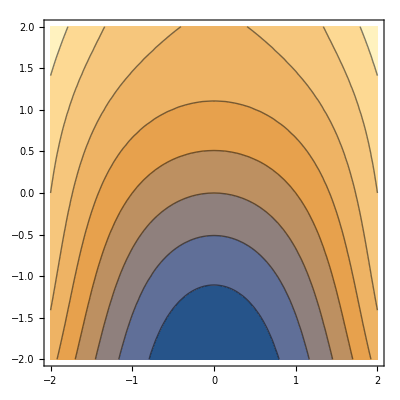

```mathematica
(*This will give the level sets for several different constants.
My examples below are for F(x,y)=x^2+y+Cos(x)Sin(y)*)
ContourPlot[x^2+y +Cos[x]Sin[y],{x,-2,2},{y,-2,2}]
```

```mathematica
(*In the example above, our curves are solutions to the equation 
2x+y'-sin(x)sin(y)+cos(x)cos(y)y'=0 
Suppose now I had an initial value problem such as 
y(Pi/2)=0.
Then I need to solve for the constant 
C=F(Pi/2,0)=(Pi^2)/2
In order to plot that solution I do the following  *)
```

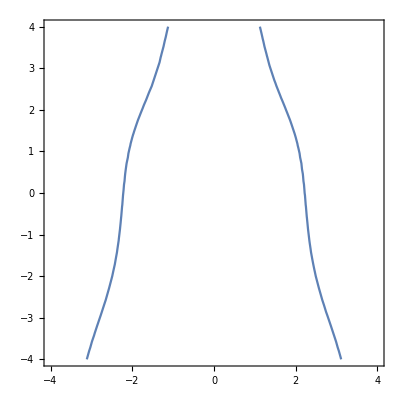

```mathematica
ContourPlot[x^2+y +Cos[x]Sin[y]==0.5(Pi)^2,{x,-4,4},{y,-4,4},Axes  ->True]
```

```mathematica
(*I think adding the axes helps understand the picture*)
```